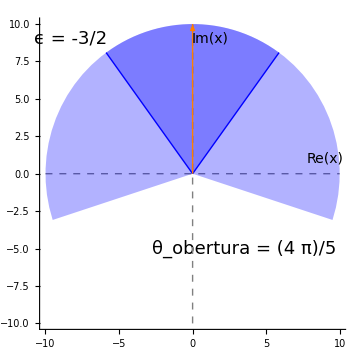

```mathematica
centroDerecha[eps_]:=-(Pi*eps)/(8+2*eps);
centroIzquierda[eps_]:=-Pi+(Pi*eps)/(8+2*eps);
amplitud[eps_]:=(2*Pi)/(4+eps);
eps=-3/2; 

Module[{cDer,cIzq,amp,radio=10},cDer=centroDerecha[eps];
cIzq=centroIzquierda[eps];
amp=amplitud[eps];
Graphics[{{GrayLevel[0.9],PointSize[0],Point[{0,0}]},(*eixos*){Gray,Dashed,Line[{{-radio,0},{radio,0}}],Line[{{0,-radio},{0,radio}}]},(*sector dret*){Opacity[0.3],Blue,Disk[{0,0},radio,{cDer-amp/2,cDer+amp/2}]},{Blue,Thick,Line[{{0,0},radio {Cos[cDer],Sin[cDer]}}]},(*sector esquerre*){Opacity[0.3],Blue,Disk[{0,0},radio,{cIzq-amp/2,cIzq+amp/2}]},{Blue,Thick,Line[{{0,0},radio {Cos[cIzq],Sin[cIzq]}}]},(*etiquetes*){Black,Text[Style["Re(x)",14],{radio-1,1}]},{Black,Text[Style["Im(x)",14],{1.2,radio-1}]},(*tall branca*){Orange,Thick,Arrowheads[Medium],Arrow[{{0,0},{0,radio}}]},{Black,Text[Style[Row[{"θ_obertura = ",NumberForm[amp,{5,3}]}],18,Background->None],{radio-6.5,-radio+5}]},{Black,Text[Style[Row[{"ϵ = ",eps}],18,Background->None],{-radio+1.7,radio-1}]}},PlotRange->{{-radio,radio},{-radio,radio}},Axes->True,ImageSize->Medium]]
```